# MATH224 Quiz 6 Q2

Trevor Swan - tcs94
DO NOT COPY OR REPRODUCE FOR ANY REASON

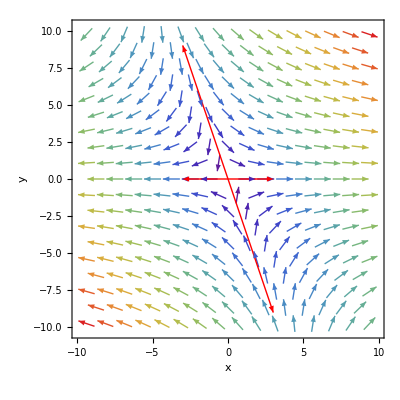

```mathematica
(* Set up plot components for part c*)
parentPlot =VectorPlot[{2*x+1*y,0*x+-1*y},{x,-10,10},{y,-10,10},VectorPoints->Medium,Axes->True,AxesLabel->{"x","y"},VectorColorFunction->"Rainbow"];
eigenVectors=Eigenvectors[{{2,1},{0,-1}}];
eigenLines1=Graphics[{Red,Arrow[{{0,0},#}]&/@(3*eigenVectors)}];
eigenLines2 = Graphics[{Red,Arrow[{{0,0},#}]&/@(-3*eigenVectors)}];
(* Display the plot for c *)
Show[parentPlot, eigenLines1, eigenLines2, PlotRange-> All]
```